```mathematica
G=1;
M1 = 10.0;
M2 = 20.0;
m = 0.25;
r21 = 1;
α1 = M2/(M1+M2);
α2 = -M1/(M1+M2);
xlim = 1;
ylim = 1;

Ueff[α_, β_]= ((G*(M1+M2)*m)/r21)*((α2/Sqrt[(α-α1)^2+β^2])  -(α1/Sqrt[(α-α2)^2+β^2]) -(1/2)*(α^2+β^2));
```

```mathematica
Plot3D[Ueff[α,β],{α,-xlim-0.5,xlim+0.5},{β,-ylim-0.5, ylim+0.5}, 
											ImageSize->Large, 
											AxesLabel->{"α","β","Ueff(α,β)"},
											PlotTheme->"Scientific"]
```

-Graphics3D-

```mathematica
DerivadaPotencialu[α_,β_] = FullSimplify[D[Ueff[α,β],α]];
DerivadaPotencialv[α_,β_] = FullSimplify[D[Ueff[α,β],β]];
```

```mathematica
Solve[{DerivadaPotencialu[α,β]==0, DerivadaPotencialv[α,β] == 0},{α,β}]
```

{{α→0.166667,β→-0.866025},{α→-1.13636,β→0.},{α→0.237418,β→0.},{α→1.24905,β→0.},{α→0.166667,β→0.866025}}

```mathematica
LagrangePoints = {{0.166667, -0.866025}, {-1.13636,0.0}, {0.237418,0.0}, {1.24905, 0.0}, {0.166667, 0.866025}};
```

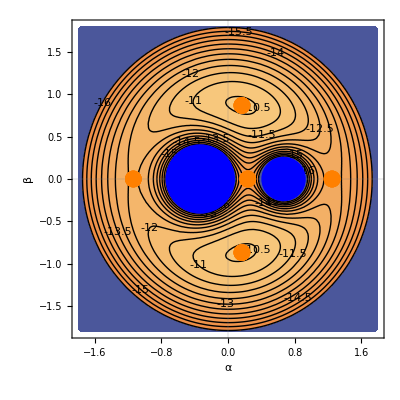

```mathematica
SetofContours = #&/@Range[-16,-10.5,0.5];
ContourPlot[Ueff[α,β],{α,-1.8,1.8},{β,-1.8,1.8}, Contours->SetofContours, ContourLabels->(Text[Framed[#3],{#1,#2},Background->LightBlue]&),
													ImageSize->Full, FrameLabel->{"α","β"},
													BaseStyle->{FontWeight->"Bold",FontSize->18},
			Epilog->{  {PointSize[0.03], Orange, Point[#] & /@ PuntosLagrange, Text["L1", PuntosLagrange[[2]],{0,3}] },
					{PointSize[0.03], Orange, Point[#] & /@ PuntosLagrange, Text["L2", PuntosLagrange[[3]],{0,-3}] },
					{PointSize[0.03], Orange, Point[#] & /@ PuntosLagrange, Text["L3", PuntosLagrange[[4]],{0,3}] },
					{PointSize[0.03], Orange, Point[#] & /@ PuntosLagrange, Text["L4", PuntosLagrange[[1]],{2,2}] },
					{PointSize[0.03], Orange, Point[#] & /@ PuntosLagrange, Text["L5", PuntosLagrange[[5]], {2,-2}] },
					{PointSize[0.08], Blue,Point[{{α1,0}}], Text["M1",{α1,0}, {4,4}]},
					{PointSize[0.13], Blue,Point[{{α2,0}}],  Text["M2",{α2,0}, {5,5}]} }, PlotTheme->"Scientific"]
```